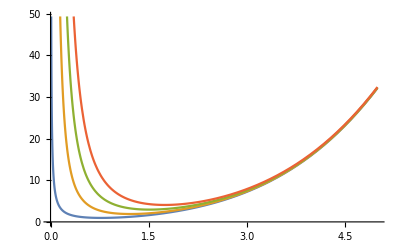

```mathematica
(*Define the function*)
V:=1/2 ω^2 r^2+1/(2 r)+(l(l+1))/(2 r^2)+λ/32 r^4

(*Choose some values for l and ω*)
l={0,1,2,3};
ω=1;
λ=1;
(*Plot V(r) for different l values*)
Plot[V,{r,0,5}]
```

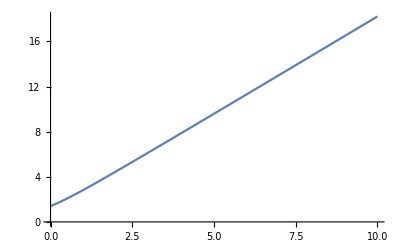

```mathematica
(*Define the constants and the equation*)
ω=2.0;
Subscript[r, 0]=1.0;
(*Define the Subscript[ω, e] function*)
Subscript[ω, e]:=(ω^2/4+1/Subscript[r, 0]^3+(3l(l+1))/Subscript[r, 0]^4)^(1/2)

(*Generate the plot for a range of l values*)
Plot[Subscript[ω, e],{l,0,10}]
```

```mathematica
l=1.0;
ω=2.0;
Solve[r^4-1/(2 ω^2)r-(l(l+1))/ω^2==0,r]
```

{{r→-0.795547},{r→-0.0441935-0.842063 ⅈ},{r→-0.0441935+0.842063 ⅈ},{r→0.883934}}

```mathematica
l=1.0;
ω=2.0;
α=(1/(8 ω^4)+√(1/(64 ω^8)+64 l^3(l+1)^3/(27 ω^6)))^(1/3);
β=-(4l(l+1))/(3 ω^2 α);
Subscript[z, 0]=α+β;
Evaluate[Subscript[z, 0]]
Evaluate[Solve[u^2-√Subscript[z, 0] u+(Subscript[z, 0]/2-1/(4 ω^2 √Subscript[z, 0]))==0,u]]
```

0.00781226

{{u→-0.795547},{u→0.883934}}

```mathematica
Evaluate[Solve[u^2+√Subscript[z, 0] u+(Subscript[z, 0]/2+1/(4 ω^2 √Subscript[z, 0]))==0,u]]
```

{{u→-0.0441935-0.842063 ⅈ},{u→-0.0441935+0.842063 ⅈ}}

```mathematica
ω=2.0;
l=1.0;
λ= 1.0;
Solve[r^6+(8 ω^2)/λ r^4-4/λ r-(8l(l+1))/λ==0, r]
```

{{r→-0.79192},{r→-0.0452152-0.846792 ⅈ},{r→-0.0452152+0.846792 ⅈ},{r→0.00195694-5.65547 ⅈ},{r→0.00195694+5.65547 ⅈ},{r→0.878437}}

```mathematica
ω=2.0;
Solve[r^3-1/(2 ω^2)==0,r]
```

{{r→-0.25-0.433013 ⅈ},{r→-0.25+0.433013 ⅈ},{r→0.5}}

```mathematica
ω=2.0;
λ=1.0;
Solve[r^3+(8 ω^2)/λ r+1/(2 ω^2)==0, r]
```

{{r→-0.00390625},{r→0.00195312-5.65686 ⅈ},{r→0.00195312+5.65686 ⅈ}}

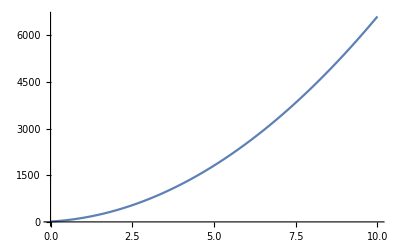

```mathematica
Subscript[r, 0]=1.0;
Subscript[λ, e][l_]:=12/Subscript[r, 0]^5(1+(5l(l+1))/Subscript[r, 0]^2);
Plot[Subscript[λ, e][l],{l,0,10}]
```